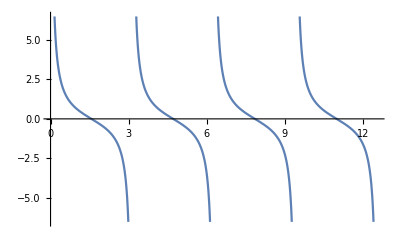

```mathematica
Plot[Cot[x],{x,0,4π}]
```

Plot in 30^° to 180^°

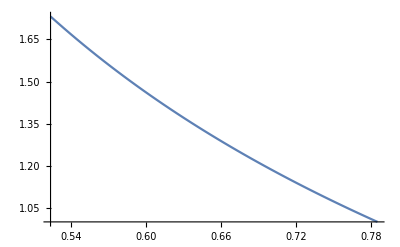

```mathematica
Plot[Cot[x],{x,π/6,π/4}]
```

Taylor Series Expansion of Cot[x]

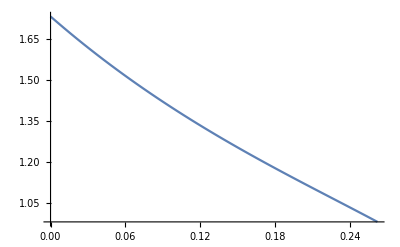

```mathematica
F[x_,δx_]:=Cot[x]-Csc[x]^2 δx/(1!)+2 Cot[x] Csc[x]^2 δx^2/(2!)+(-4 Cot[x]^2 Csc[x]^2-2 Csc[x]^4)δx^3/(3!)+(8 Cot[x]^3 Csc[x]^2+16 Cot[x] Csc[x]^4)δx^4/(4!)+(-16 Cot[x]^4 Csc[x]^2-88 Cot[x]^2 Csc[x]^4-16 Csc[x]^6)δx^5/(5!);
Plot[F[π/6,δx],{δx,0,(π/4-π/6)}]
```

```mathematica
D[Cot[x],{x,5}]
```

-16 Cot[x]^4 Csc[x]^2-88 Cot[x]^2 Csc[x]^4-16 Csc[x]^6

```mathematica
Example-2
```

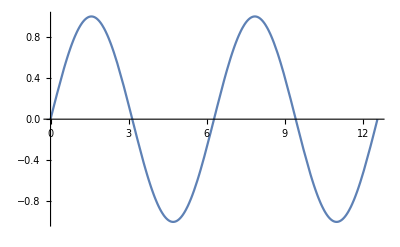

```mathematica
Plot[Sin[x],{x,0,4π}]
```

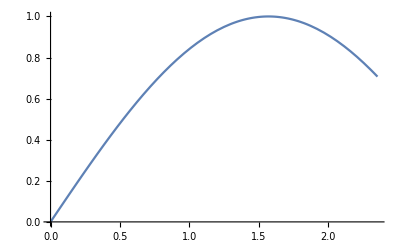

```mathematica
Plot[Sin[x],{x,0,(3π)/4}]
```

```mathematica
F[0,a]
```

a-a^3/6+a^5/120-a^7/5040+a^9/362880

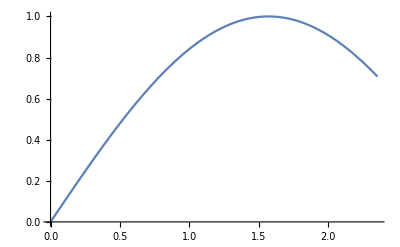

```mathematica
F[x_,δx_]:=Sin[x]+(Cos[x]) δx/(1!)+(-Sin[x]) δx^2/(2!)+(-Cos[x])δx^3/(3!)+(Sin[x])δx^4/(4!)+(Cos[x])δx^5/(5!)+(-Sin[x]) δx^6/(6!)+(-Cos[x])δx^7/(7!)+(Cos[x])δx^9/(9!);
Plot[F[0,δx],{δx,0,(3π)/4}]
```

```mathematica
D[Sin[x],{x,1}]
```

Cos[x]